## GRIN lens heat test

Analysis of the FORT and 780 beams in the atom focal plane prior to the 2021 refactor.

## setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
```

## analysis

```mathematica
pixels780 = 11.9; (*pixels per microns in object plane, using Urban imaging camera with PointGrey CCD*)
```

```mathematica
StringJoin[{"hel","lo"}]
```

hello

```mathematica
imgAfter = Table[ColorConvert[Import[StringJoin[".\\GRIN_lens_heat_test\\Images_after_baking\\",fname,".bmp"]],"grayscale"],{fname,{"01","02","03","04","05","06","07","08","09","10"}}];
```

```mathematica
imgBefore = Table[ColorConvert[Import[StringJoin[".\\GRIN_lens_heat_test\\Images_before_baking\\",fname,".bmp"]],"grayscale"],{fname,{"01- spot1","02- spot2","03- spot3","04- spot4","05- spot5","06- spot6","07- spot7","08- spot8","09- spot9","10- spot10"}}];
```

```mathematica
ImageData[imgAfter[[1]]]//Dimensions
```

{960,1280}

Images before the bake

```mathematica
data = Table[ImageData[imgBefore[[i]]][[350;;590,500;;880]]-0.075,{i,Range[Length[imgAfter]]}];
xmax =880-500;
model = A  Exp[(-2(x-μ)^2)/σ^2];
Image[data[[1]]]
```

-Graphics-

-Graphics-

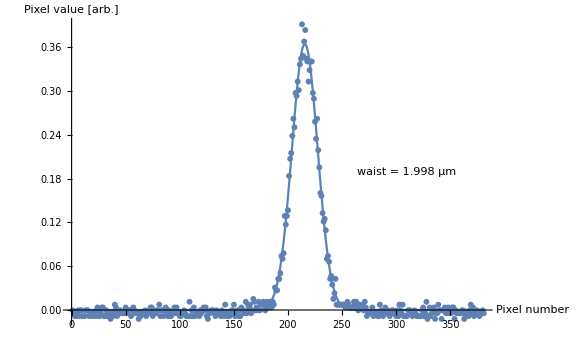

-Graphics-

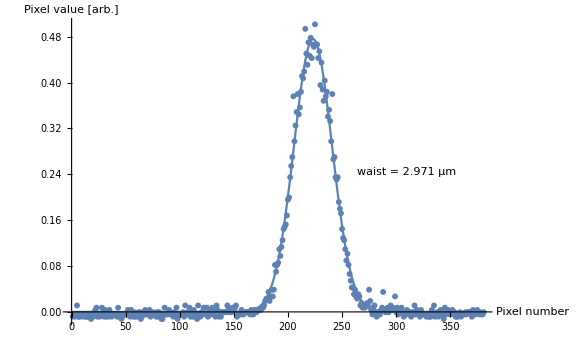

-Graphics-

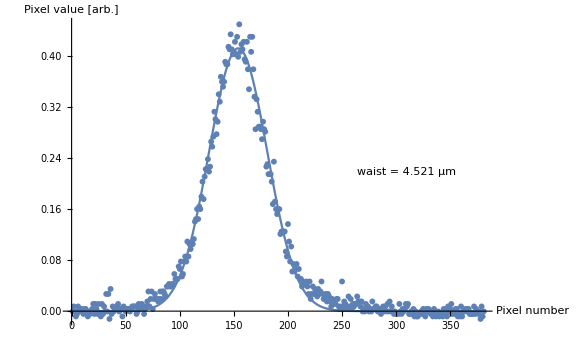

-Graphics-

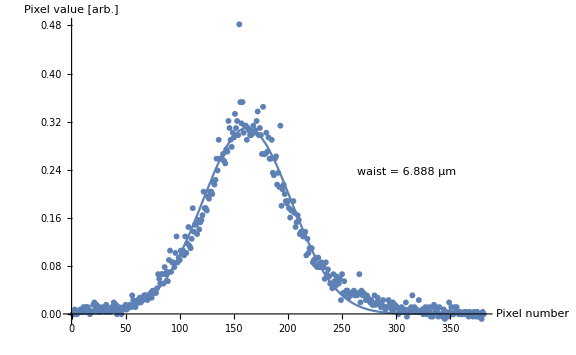

-Graphics-

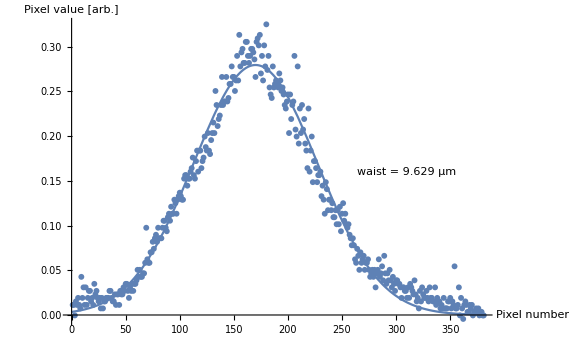

-Graphics-

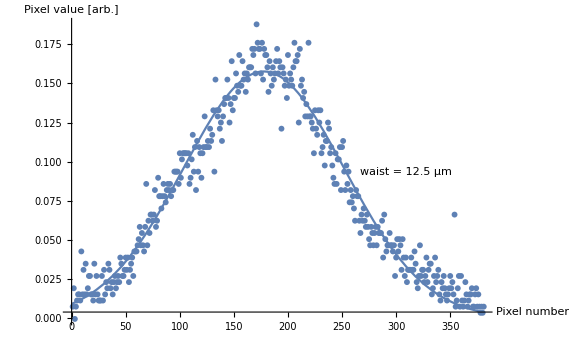

```mathematica
waistsBefore = {};
slice ={120,130,143,150,155,155};
For[i=1,i< 7,i++,
Print[Show[Image[data[[i]]],ListPlot[{{0,250-slice[[i]]},{350,250-slice[[i]]}},Joined->True,PlotStyle->Red],Frame-> True]];
(*Print[ListPlot[data[[i]][[slice[[i]],;;]],PlotRange->All]];*)
(*do a fit to the slice*)
fit =FindFit[data[[i]][[slice[[i]],;;]],model,{{μ,200},σ,A},x];
Print[Show[Plot[model/.fit,{x,0,xmax},PlotRange->All,PlotLegends-> Placed[ToString[StringForm["waist = `` μm",NumberForm[Values[fit[[2]]]/pixels780,4]]],{0.8,0.5}]],ListPlot[data[[i]][[slice[[i]],;;]]],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize-> Large,
LabelStyle-> Directive[Black, FontSize-> 14],ImageSize-> Medium]];
AppendTo[waistsBefore,Values[fit[[2]]]/pixels780];
]
```

Images after the bake

```mathematica
data = Table[ImageData[imgAfter[[i]]][[80;;330,370;;740]]-0.075,{i,Range[Length[imgAfter]]}];
xmax =740-370;
model = A  Exp[(-2(x-μ)^2)/σ^2];
```

-Graphics-

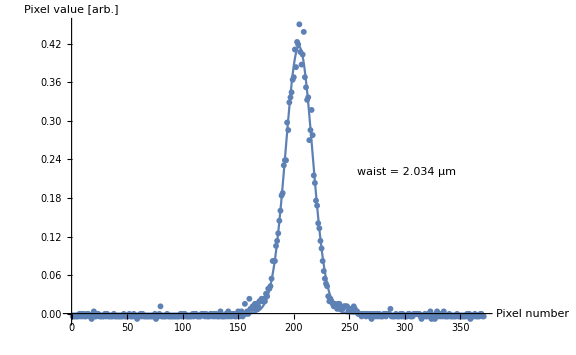

-Graphics-

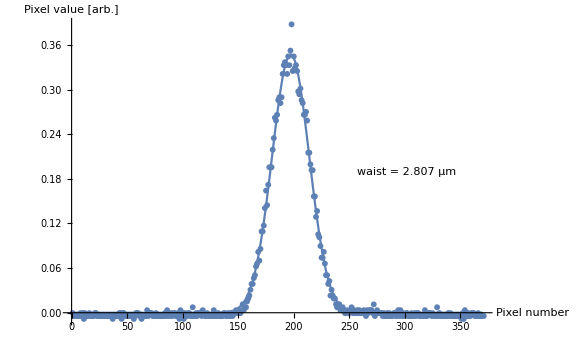

-Graphics-

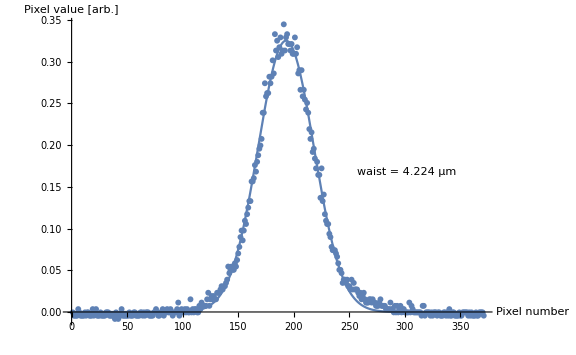

-Graphics-

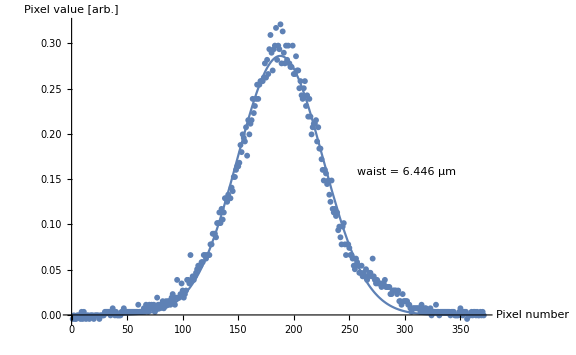

-Graphics-

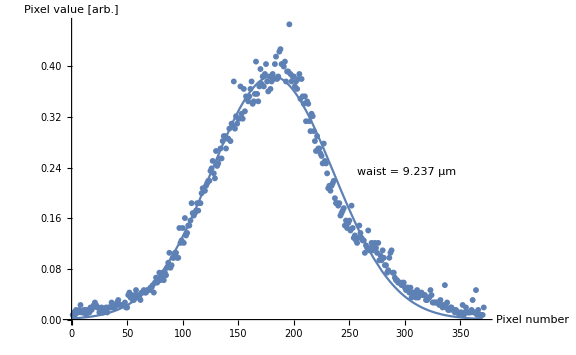

-Graphics-

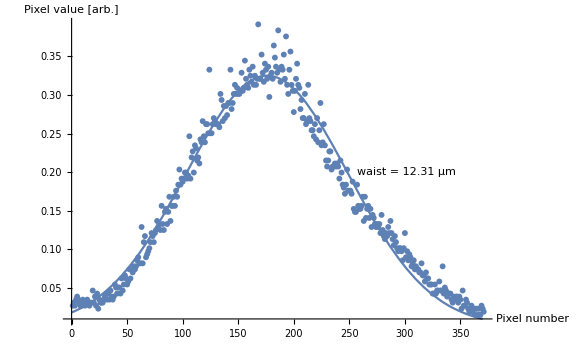

```mathematica
waistsAfter = {};
slice ={162,155,143,135,120,130};
For[i=1,i< 7,i++,
Print[Show[Image[data[[i]]],ListPlot[{{0,250-slice[[i]]},{350,250-slice[[i]]}},Joined->True,PlotStyle->Red],Frame-> True]];
(*Print[ListPlot[data[[i]][[slice[[i]],;;]],PlotRange->All]];*)
(*do a fit to the slice*)
fit =FindFit[data[[i]][[slice[[i]],;;]],model,{{μ,200},σ,A},x];
Print[Show[Plot[model/.fit,{x,0,xmax},PlotRange->All,PlotLegends-> Placed[ToString[StringForm["waist = `` μm",NumberForm[Values[fit[[2]]]/pixels780,4]]],{0.8,0.5}]],ListPlot[data[[i]][[slice[[i]],;;]]],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize-> Large,
LabelStyle-> Directive[Black, FontSize-> 14],ImageSize-> Medium]];
AppendTo[waistsAfter,Values[fit[[2]]]/pixels780];
]
```

Plot the waists pre and post bake

```mathematica
Length[waistsAfter]
```

6

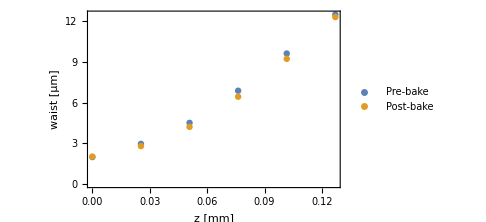

```mathematica
zsteps = Range[0,5]*0.25*2.54/25;
Show[ListPlot[{Transpose@{zsteps,waistsBefore},Transpose@{zsteps,waistsAfter}},PlotLegends->{"Pre-bake","Post-bake"},FrameLabel->{"z [mm]","waist [μm]"}]
(*Plot[waistsBefore[[1]] √(1+((z*10^3 0.78)/(π waistsBefore[[1]]^2))^2),{z,0,zsteps[[-1]]}]*)]
```

```mathematica
ListPlot[waistsBefore]
```

-Graphics-

```mathematica
waistsBefore[[1]]
```

1.99843

```mathematica
wa
```